```mathematica
s1 = 0.8;(*saturation parameter 397*)
s2 = 10; (*saturation parameter 866*)
```

```mathematica
H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});
H1=H/.{Subscript[Δ, g]->-10,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2}
```

{{-10,6.47002,0},{6.47002,0,1.72177},{0,1.72177,Δ_r}}

```mathematica
Subscript[C, 1]=√(22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];
```

```mathematica
(*Lindblad eqn*)
```

```mathematica
scanred[δ_]:=Module[{r,H=H1/.{Subscript[Δ, r]->δ},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
]
```

```mathematica
scanred[-10]
```

{0.066134,-9.57113×10^-17,0.933866}

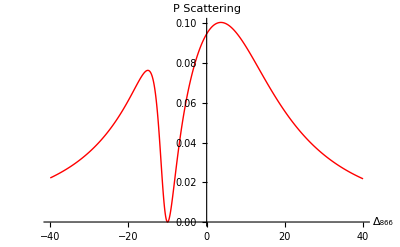

```mathematica
data=Table[{x,scanred[x]},{x,-40,40,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Δ_866","P Scattering"}]
```

```mathematica
foo[30]
```

foo[30]

```mathematica
H2
```

{{Δ_g,6.47002,0},{6.47002,0,1.72177},{0,1.72177,5}}

```mathematica
H2=H/.{Subscript[Δ, r]->5,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2};
scanblue[δ_]:=Module[{r,H=H2/.{Subscript[Δ, g]->δ},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
];

scanblue[-10]
```

{0.576766,0.0998029,0.323431}

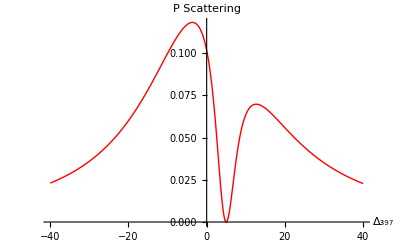

```mathematica
data2=Table[{x,scanblue[x]},{x,-40,40,0.1}];
ListLinePlot[{{data2⟦All,1⟧,data2⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Δ_397","P Scattering"}]
```

```mathematica
s1 = 0.8;(*saturation parameter 397*)
```

```mathematica
H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});
```

```mathematica
H0=H/.{Subscript[Δ, g]->-10,Subscript[Δ, r]->5,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2}
```

{{-10,6.47002,0},{6.47002,0,0.544472 √s2},{0,0.544472 √s2,5}}

```mathematica
Subscript[C, 1]=√(22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];
```

```mathematica
scanredintensity[s_]:=Module[{r,H=H0/.{s2->s},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
]
```

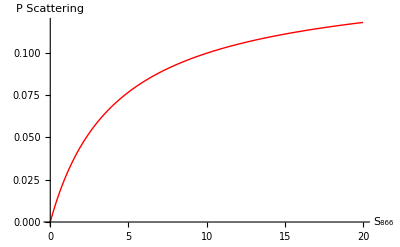

```mathematica
data=Table[{s,scanredintensity[s]},{s,0,20,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"S_866","P Scattering"}]
```

```mathematica
(*Simulation of scattering rate vs 866 satuation parameter*)
```

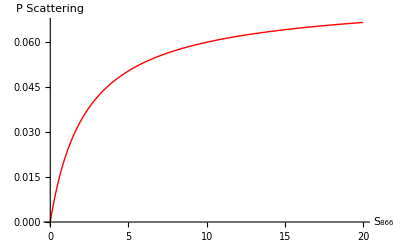

```mathematica
s1 = 0.8(*saturation parameter 397*);H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});H0=H/.{Subscript[Δ, g]->-20,Subscript[Δ, r]->5,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2};Subscript[C, 1]=√(22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];scanredintensity[s_]:=Module[{r,H=H0/.{s2->s},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
];data=Table[{s,scanredintensity[s]},{s,0,20,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"S_866","P Scattering"}]
```

```mathematica
1000/532-1000/397
```

-33750/52801

```mathematica
N[-33750/52801]
```

-0.639192

```mathematica
1000/397-1000/393
```

-4000/156021

```mathematica
N[-4000/156021]
```

-0.0256376

```mathematica
N[(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))]
```

4.69809×10^-37

```mathematica
(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))*(2*100*10^-3)/(Pi*(5*10^-6)^2)*Exp[(-2*r^2)/((5*10^-6)^2)]
```

(471971340739 ⅇ^(-80000000000 r^2))/(4050000000000000000000000000000000000 π^4)

```mathematica
Series[(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))*(2*100*10^-3)/(Pi*(5*10^-6)^2)*Exp[(-2*r^2)/((5*10^-6)^2)],{r,0,3}]
```

471971340739/(4050000000000000000000000000000000000 π^4)-(471971340739 r^2)/(50625000000000000000000000 π^4)+O[r]^4

```mathematica
1/2*(40*1.6605402^-27)
```

```mathematica
√(471971340739/(50625000000000000000000000 π^4)/(1/2*(40*1.6605402^-27)))
```

2.05744×10^-6

```mathematica
Series[(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))*(2*100*10^-3)/(Pi*(5*10^-6)^2)*Exp[(-2*r^2)/((5*10^-6)^2)],{r,0,3}]
```

```mathematica
Series[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(280*10^-9))^3)*(2*Pi*41.8*10^6)/(2*Pi*275*10^9)*(190*10^-3)/((7*10^-6)^2)*(Exp[(-2*r^2)/((7*10^-6)^2)]),{r,0,3}]
```

5.21598×10^-25-2.12897×10^-14 r^2+O[r]^4

```mathematica
√((2.1289698615561172*^-14)/(1/2*(24*1.6605402^-27)))/2*Pi
```

```mathematica
1/0.0000622273
```

16070.1

```mathematica
(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(280*10^-9))^3)*(2*Pi*41.8*10^6)/(2*Pi*275*10^9)*(190*10^-3)/((7*10^-6)^2)/(1.380649*10^-23)
```

0.0377792

```mathematica
(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))*(2*190*10^-3)/(Pi*(7*10^-6)^2)/(1.380649*10^-23)
```

0.0000839992

```mathematica
1/(7*10^-9)
```

1000000000/7

```mathematica
N[1000000000/7]
```

1.42857×10^8

```mathematica
2*Pi*41.8*10^6
```

2.62637×10^8

```mathematica
N[2*Pi*275*10^9]
```

1.72788×10^12

```mathematica
N[2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9))]
```

1.2048493633679

```mathematica
Series[(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))*(2*100*10^-3)/(Pi*(5*10^-6)^2),{r,0,3}]
```

```mathematica
√(N[(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(397*10^-9))^3)*(1/(7*10^-9))/(2*Pi*(-(3*10^8)/(532*10^-9)+(3*10^8)/(397*10^-9)))*(2*100*10^-3)/(Pi*(1*10^-6)^2)]*24/(40*N[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(280*10^-9))^3)*(2*Pi*41.8*10^6)/(2*Pi*275*10^9)*(190*10^-3)/((7*10^-6)^2)]))
```

0.185485

```mathematica
(3*10^8)/(397*10^-9)-(3*10^8)/(398*10^-9)
```

150000000000000000/79003

```mathematica
N[150000000000000000/79003]
```

1.89866×10^12

```mathematica
N[-150000000000000000/199]
```

-7.53769×10^14

```mathematica
(3*10^8)/(369*10^-9)-(3*10^8)/(375*10^-9)
```

1600000000000000/123

```mathematica
N[1600000000000000/123]
```

1.30081×10^13

```mathematica
N[55000000000000000/2337]
```

2.35344×10^13

```mathematica
N[10000000000000000/4551]
```

2.19732×10^12

```mathematica
N[4075000000000000000/16359]
```

2.49098×10^14

```mathematica
2*Pi*165*1000*√((24*N[(3*Pi*(3*10^8)^2)/(2*(2*Pi*(3*10^8)/(369.5*10^-9))^3)*(1/(7*10^-9))/(15*10^12)*(2*156*10^-6)/(Pi*(0.5*10^-6)^2)])/(173.04*N[(3*(3*10^8)^2)/((2*Pi*(3*10^8)/(280*10^-9))^3)*(2*Pi*19.6*10^6)/(2*Pi*275*10^9)*(190*10^-3)/((7*10^-6)^2)]))
```

85829.8